```mathematica
(*Bloque para cargar MaTeX*)
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs10.03.0\\bin\\gswin64c.exe"];
ConfigureMaTeX["pdfLaTeX" -> "C:\\texlive\\2024\\bin\\windows\\pdflatex.exe"]
<<MaTeX`;
MaTeX["x^2"]
```

ConfigureMaTeX[pdfLaTeX→C:\texlive\2024\bin\windows\pdflatex.exe]

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

ConfigureMaTeX::shdw: Symbol ConfigureMaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

-Graphics-

```mathematica
ν=1/3;
```

Relacion Original simetrica

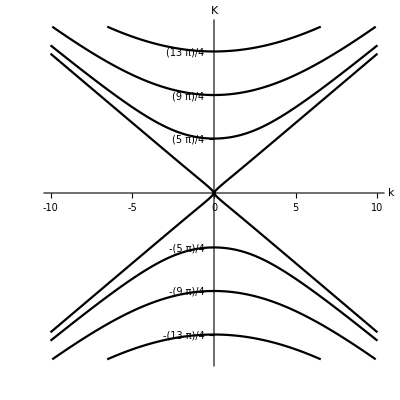

```mathematica
ContourPlot[Sqrt[Kw^2-k^2]*(Kw^2+(1-ν)k^2)^2 *Cosh[Sqrt[Kw^2+k^2]]*Sin[Sqrt[Kw^2-k^2]]-
Sqrt[Kw^2+k^2]*(Kw^2-(1-ν)k^2)^2 *Sinh[Sqrt[Kw^2+k^2]]*Cos[Sqrt[Kw^2-k^2]]==0,{k,-10,10},{Kw,-12,12}, PlotTheme->"Monochrome", Frame->False,Axes->True,AxesLabel->{k,K}, Ticks->{{-10,-5,0,5,10},{-5Pi/4,-9Pi/4, -13Pi/4,5Pi/4,9Pi/4, 13Pi/4}}, MaxRecursion->5]
```

Relacion original antisimetrica

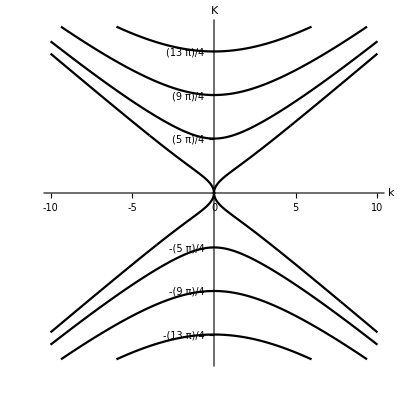

```mathematica
ContourPlot[Sqrt[Kw^2+k^2]*(Kw^2-(1-ν)k^2.)^2 *Sin[Sqrt[Kw^2-k^2]]-
Sqrt[Kw^2-k^2]*(Kw^2+(1-ν)k^2)^2 *Tanh[Sqrt[Kw^2+k^2]]*Cos[Sqrt[Kw^2-k^2]]==0.,{k,-10,10},{Kw,-12,12}, MaxRecursion->6, PerformanceGoal->"Quality", PlotTheme->"Monochrome", Frame->False,Axes->True,AxesLabel->{k,K}, Ticks->{{-10,-5,0,5,10},{-5Pi/4,-9Pi/4, -13Pi/4,5Pi/4,9Pi/4, 13Pi/4}}]
```

Relacion de dispersion simetrica

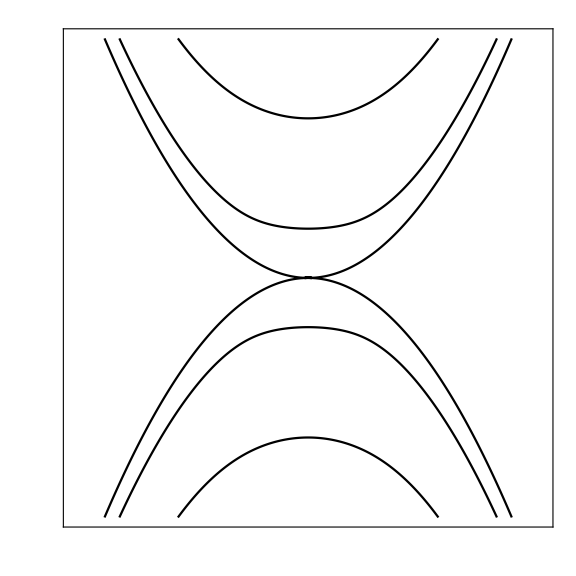

```mathematica
graficaSimetrica=ContourPlot[Sqrt[Abs[w]-k^2]*(Abs[w]+(1-ν)k^2)^2 *Cosh[Sqrt[Abs[w]+k^2]/2]*Sin[Sqrt[Abs[w]-k^2]/2]-
Sqrt[Abs[w]+k^2]*(Abs[w]-(1-ν)k^2)^2 *Sinh[Sqrt[Abs[w]+k^2]/2]*Cos[Sqrt[Abs[w]-k^2]/2]==0,{k,-20,20},{w,-300,300}, PlotTheme->"Monochrome", MaxRecursion->5, ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}]
```

```mathematica
Export["simetrica.pdf", graficaSimetrica]
```

simetrica.pdf

```mathematica
Export["antisimetrica.pdf", antisimetrica]
```

antisimetrica.pdf

Relación de Dispersión Antisimétrica

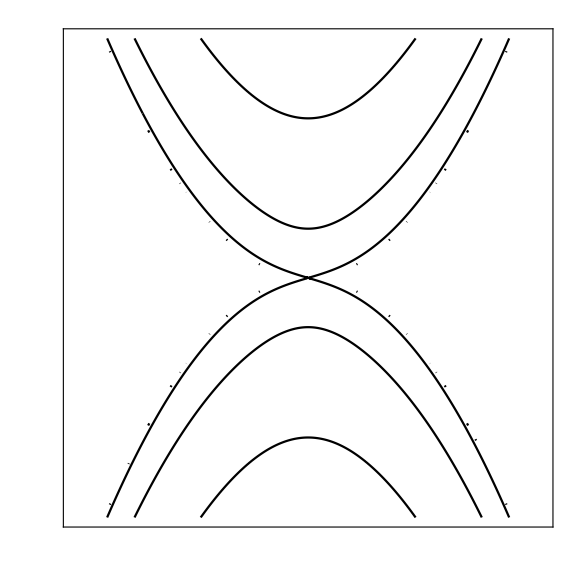

```mathematica
antisimetrica=ContourPlot[Sqrt[Abs[w]+k^2]*(Abs[w]-(1-ν)k^2)^(2) *Cosh[Sqrt[Abs[w]+k^2]/2]*Sin[Sqrt[Abs[w]-k^2]/2]-
Sqrt[Abs[w]-k^2]*(Abs[w]+(1-ν)k^2)^(2) *Sinh[Sqrt[Abs[w]+k^2]/2]*Cos[Sqrt[Abs[w]-k^2]/2]==0,{k,-20,20},{w,-300,300}, PlotTheme->"Monochrome", MaxRecursion->5,  ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}]
```

```mathematica
derivadaImplicitaAntiS =Simplify[ImplicitD[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0, w, k]];(*Calculo simbolico de la derivada implicita del caso antisimetrico dw/dk*)
```

```mathematica
derivadaImplicita2AntiS = ImplicitD[derivadaImplicitaAntiS, Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0, w, k];
(*Calculo simbolico de la segunda derivada implicita del caso antisimetrico d^2w/dk^2*)
```

```mathematica
derivadaImplicitaSim=Simplify[ImplicitD[w,Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]]*Sin[Sqrt[w-k^2]]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]]*Cos[Sqrt[w-k^2]]==0, w, k]];
(*Calculo simbolico de la derivada implicita del caso simetrico dw/dk*)
```

```mathematica
derivadaImplicita2Sim =ImplicitD[derivadaImplicitaSim, Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]]*Sin[Sqrt[w-k^2]]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]]*Cos[Sqrt[w-k^2]]==0, w, k];
(*Calculo simbolico de la segunda derivada implicita del caso antisimetrico d^2w/dk^2*)
```

```mathematica
(*Masa efectiva caso Antisimetrico cerca de ω = 200*)Re[With[{ k=0.0}, Evaluate[1/derivadaImplicita2AntiS]]/.With[{k=0.0}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]+200.0}, WorkingPrecision->20]]]
```

FindRoot::precw: The precision of the argument function ((0.+w)^(5/2) Cosh[(√(0.+w))/2] Sin[(√(0.+w))/2]-(0.+w)^(5/2) Cos[(√(0.+w))/2] Sinh[(√(0.+w))/2]==0) is less than WorkingPrecision (20.).

0.381319

```mathematica
(*Masa efectiva caso Antisimetrico cerca de ω = 60*)Re[With[{ k=0.0}, Evaluate[1/derivadaImplicita2AntiS]]/.With[{k=0.0}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]+60.0}, WorkingPrecision->MachinePrecision]]]
```

0.320047

```mathematica
Manipulate[(*Evaluacion de la masa efectiva en el origen, caso antisimetrico*)
Re[With[{ k=waveN}, Evaluate[1/derivadaImplicita2AntiS]]/.With[{k=waveN}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]+0.0}, WorkingPrecision->14]]],
{waveN, 10^-Range[7] }]
```

FindRoot::nlnum: The function value {-5.×10^-8 (1.×10^-7+1.×10^-14 (1.+Times[«2»]))^2+5.×10^-8 (1.×10^-7+1.×10^-14 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-7}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/10000000]+0.},WorkingPrecision→14]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-5.×10^-8 (1.×10^-7+1.×10^-14 (1.+Times[«2»]))^2+5.×10^-8 (1.×10^-7+1.×10^-14 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-7}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/10000000]+0.},WorkingPrecision→14]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-5.×10^-8 (1.×10^-7+1.×10^-14 (1.+Times[«2»]))^2+5.×10^-8 (1.×10^-7+1.×10^-14 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-7}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/10000000]+0.},WorkingPrecision→14]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-5.×10^-8 (1.×10^-7+1.×10^-14 (1.+Times[«2»]))^2+5.×10^-8 (1.×10^-7+1.×10^-14 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-7}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/10000000]+0.},WorkingPrecision→14]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-5.×10^-8 (1.×10^-7+1.×10^-14 (1.+Times[«2»]))^2+5.×10^-8 (1.×10^-7+1.×10^-14 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-7}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/10000000]+0.},WorkingPrecision→14]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-5.×10^-8 (1.×10^-7+1.×10^-14 (1.+Times[«2»]))^2+5.×10^-8 (1.×10^-7+1.×10^-14 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-7}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/10000000]+0.},WorkingPrecision→14]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(*Masa efectiva caso Antisimetrico cerca de ω = -60*)Re[With[{ k=0.0}, Evaluate[1/derivadaImplicita2AntiS]]/.With[{k=0.0}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]-60.0}, WorkingPrecision->MachinePrecision]]]
```

-0.320047

```mathematica
(*Masa efectiva caso Antisimetrico cerca de ω = 200*)Re[With[{ k=0.0}, Evaluate[1/derivadaImplicita2AntiS]]/.With[{k=0.0}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]-200.0}, WorkingPrecision->20]]]
```

FindRoot::precw: The precision of the argument function ((0.+w)^(5/2) Cosh[(√(0.+w))/2] Sin[(√(0.+w))/2]-(0.+w)^(5/2) Cos[(√(0.+w))/2] Sinh[(√(0.+w))/2]==0) is less than WorkingPrecision (20.).

-0.381319

```mathematica
(*Masa efectiva caso simetrico cerca de ω = 200*)Re[With[{ k=0.0}, Evaluate[1/derivadaImplicita2Sim]]/.With[{k=0.0}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]+200.0}, WorkingPrecision->MachinePrecision]]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-7.56248

```mathematica
Re[With[{ k=0.0}, Evaluate[1/derivadaImplicita2Sim]]/.With[{k=0.0}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]+60.0}, WorkingPrecision->MachinePrecision]]]
```

-4.72767

```mathematica
Manipulate[(*Evaluacion de la masa efectiva en el origen, caso antisimetrico*)
Re[With[{ k=waveN}, Evaluate[1/derivadaImplicita2Sim]]/.With[{k=waveN}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]+0.0}, WorkingPrecision->20]]],
{waveN, 10^-Range[9] }]
```

FindRoot::nlnum: The function value {5.×10^-10 (1.×10^-9+1.×10^-18 (1.+Times[«2»]))^2-5.×10^-10 (1.×10^-9+1.×10^-18 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-9}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/1000000000]+0.},WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {5.×10^-10 (1.×10^-9+1.×10^-18 (1.+Times[«2»]))^2-5.×10^-10 (1.×10^-9+1.×10^-18 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-9}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/1000000000]+0.},WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {5.×10^-10 (1.×10^-9+1.×10^-18 (1.+Times[«2»]))^2-5.×10^-10 (1.×10^-9+1.×10^-18 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-9}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/1000000000]+0.},WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {5.×10^-10 (1.×10^-9+1.×10^-18 (1.+Times[«2»]))^2-5.×10^-10 (1.×10^-9+1.×10^-18 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-9}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/1000000000]+0.},WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {5.×10^-10 (1.×10^-9+1.×10^-18 (1.+Times[«2»]))^2-5.×10^-10 (1.×10^-9+1.×10^-18 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-9}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/1000000000]+0.},WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {5.×10^-10 (1.×10^-9+1.×10^-18 (1.+Times[«2»]))^2-5.×10^-10 (1.×10^-9+1.×10^-18 (-1.+ν))^2} is not a list of numbers with dimensions {1} at {w} = {1.×10^-9}.

ReplaceAll::reps: {FindRoot[((√(«1») Power[«2»]) Cosh[Times[«2»]]) Sin[√(«1») Power[«2»]]-(«2» Sinh[«1»]) Cos[Times[«2»]]==0,{w,Abs[1/1000000000]+0.},WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(*Masa efectiva Caso simetrico ω=-60*)Re[With[{ k=0.0}, Evaluate[1/derivadaImplicita2Sim]]/.With[{k=0.0}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]-60.0}, WorkingPrecision->MachinePrecision]]]
```

4.72767

```mathematica
(*Masa efectiva Caso simetrico ω=-200*)Re[With[{ k=0.0}, Evaluate[1/derivadaImplicita2Sim]]/.With[{k=0.0}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]-200.0}, WorkingPrecision->MachinePrecision]]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

7.56248

```mathematica
NSolve
```